# Global settings

```mathematica
kernel=KernelConfiguration["ssh://strelda@ipnp36.troja.mff.cuni.cz"]
```

KernelConfiguration[…]

```mathematica
CloseKernels[];
```

```mathematica
LaunchKernels[kernel,16]
```

{strelda@ipnp36.troja.mff.cuni.cz,strelda@ipnp36.troja.mff.cuni.cz,strelda@ipnp36.troja.mff.cuni.cz,strelda@ipnp36.troja.mff.cuni.cz,strelda@ipnp36.troja.mff.cuni.cz,strelda@ipnp36.troja.mff.cuni.cz,strelda@ipnp36.troja.mff.cuni.cz,strelda@ipnp36.troja.mff.cuni.cz,strelda@ipnp36.troja.mff.cuni.cz,strelda@ipnp36.troja.mff.cuni.cz,strelda@ipnp36.troja.mff.cuni.cz,strelda@ipnp36.troja.mff.cuni.cz,strelda@ipnp36.troja.mff.cuni.cz,strelda@ipnp36.troja.mff.cuni.cz,strelda@ipnp36.troja.mff.cuni.cz,strelda@ipnp36.troja.mff.cuni.cz}

# Basic functions and settings

```mathematica
<<CompiledFunctionTools`
<<MaTeX`
Needs["NumericalCalculus`"]
ParallelNeeds["NumericalCalculus`"]
ResourceFunction["PlotGrid"];
compileOptions={CompilationTarget->"C",RuntimeOptions->{"EvaluateSymbolically"->False,"CatchMachineUnderflow"->False,"CatchMachineOverflow"->False}};
font={BaseStyle->{FontFamily->"Times New Roman",FontSize->12},AxesStyle->Directive[FontSize->12],TicksStyle->Directive[FontSize->12],LabelStyle->{FontFamily->"Times New Roman",FontSize-> 12}};
densityPlotOptions={PlotRange->Full,PlotLegends->Automatic,FrameLabel->MaTeX/@{"\\kappa","\\chi"},Evaluate@font,ColorFunction->GrayLevel};
densityPlotOptionsWithoutLegend={PlotRange->Full,FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"Temperature"};
densityPlotOptionsWithLegend={PlotRange->Full,Evaluate@font,FrameLabel->MaTeX/@{"\\lambda","\\chi"},ColorFunction->"Temperature"};
plotOptions={Frame->True,PerformanceGoal->"Quality",Evaluate@font,FrameLabel->MaTeX/@{"\\kappa","\\chi"},Axes->False};
$PlotTheme="Scientific";
```

```mathematica
density1={Evaluate@font,ColorFunction->"Temperature"};
density2={PerformanceGoal->"Quality",FrameLabel->MaTeX/@{"\\kappa","\\chi"},Evaluate@font,ColorFunction->"Temperature",PlotLegends->True,ImageSize->310};
density3={PerformanceGoal->"Quality",FrameLabel->MaTeX/@{"\\kappa","\\chi"},Evaluate@font,ColorFunction->"Temperature",PlotLegends->True,ImageSize->410};
export1={"AllowRasterization"->True,ImageResolution->800};
plot1={Frame->True,Evaluate@font,Axes->False};
plot2={Frame->True,PerformanceGoal->"Quality",ImageSize->310,Evaluate@font,Axes->False,PlotStyle->Thickness[0.004]};
```

```mathematica
ggSize=360;
optDen={Evaluate@font,PlotRange->Full,PlotLegends->False,FrameLabel->MaTeX/@{"\\kappa","\\chi"},ColorFunction->ColorData[{"TemperatureMap",{-π/2,π/2}}],PlotPoints->30,FrameTicks->{{Range[-6,6,0.5],None},{Range[-6,6,2],None}},ColorFunctionScaling->False};
```

```mathematica
cross=Graphics[{Line[{{-1,-1},{1,1}}],Line[{{1,-1},{-1,1}}]}];
```

```mathematica
getTimesFromSolve[list_]:=Table[list[[i,1,1,2,1,1,2]],{i,1,Dimensions[list][[1]]}]
PlotSols[solMulti_,col_:"Green"]:=Table[ParametricPlot[
{λ[t],χ[t]}/.solMulti[[i]],{t,0,getTimesFromSolve[solMulti][[i]]}
,PlotRange->All,Frame->True,Evaluate@plotOptions,PlotStyle->{ToExpression@col,Thickness[0.002]},AspectRatio->1],{i,1,Dimensions[solMulti][[1]]}]

GetMaxTimeFromSolve[sol_]:=sol[[1,1,2,1,1,2]];
GetMinMaxFromSolution[sol_]:=Module[{tmax,list,n},
tmax=GetMaxTimeFromSolve[sol];
n=100;
list=Table[Max[√(λ'[t]^2+χ'[t]^2)/.sol],{t,tmax/n,(n-1)tmax/n,tmax/n}];
{Min@list,Max@list}
];
```

```mathematica
σ0={{1,0},{0,1}};
σ1={{0,1},{1,0}};
σ2={{0,-I},{I,0}};
σ3={{1,0},{0,-1}};
σ={σ0,σ1,σ2,σ3};
```

```mathematica
qptA[λ_]=If[λ<1,√((λ-1)/(λ-2)),0];
qpt[λ_?NumericQ]:=If[λ<1,√((λ-1)/(λ-2)),0];
qptC=Compile[{{λ,_Real}},√((λ-1)/(λ-2)),Evaluate@compileOptions];
Phase1[λ_,χ_]:=Abs@χ<qpt[λ]
```

```mathematica
numInnn[nn_]:=If[EvenQ[nn],nn/2,(nn-1)/2]
χg[nn_]:=If[EvenQ[nn],
Table[√(nn/(nn-1+2k)),{k,1,numInnn[nn]}],
Table[√(nn/(nn+2k)),{k,1,numInnn[nn]}]
]
λg[nn_]:=If[EvenQ[nn],
Table[(-nn+2k-1)/(2k-1),{k,1,numInnn[nn]}],
Table[(-nn+2k)/(2k),{k,1,numInnn[nn]}]
]
diabolicPoints[nn_]:=Transpose@{λg[nn],χg[nn]}
```

```mathematica
PlotWithLegend[plot_,legend_]:=Grid[{{Item[plot]},{Item[Row[{Spacer[35],legend}],Alignment->Center]}},Spacings->{Automatic,{1,Scaled[0]}}]
```

```mathematica
pltLabel[text_String,px_,py_]:=Graphics[Text[Style[text,Evaluate@font,14],Scaled[{px,py}]]];
chiText[px_,py_,text_"\\chi"]:=Graphics[Text[Style[Rotate[MaTeX[text],π/2],Evaluate@font],Scaled[{px,py}]]]
TextPos[px_,py_,text_,rot_:π/2]:=Graphics[Text[Style[Rotate[MaTeX[text],rot],Evaluate@font],Scaled[{px,py}]]]
```

```mathematica
sign[x_]:=2 HeavisideTheta[x]-1
```

```mathematica
extract[tab_]:=Module[{d,exampleCoord,varNames},
d=Dimensions@tab;
exampleCoord=tab[[1,1,3]];
varNames=exampleCoord[[#,1]]&/@Range[Length@exampleCoord];
Flatten[Table[Flatten@{tab[[i,j]][[1;;2]],#/.tab[[i,j]][[3]]},{i,1,d[[1]]},{j,1,d[[2]]}],1]&/@varNames
]
extract2D[tab_]:=Module[{d,exampleCoord,varNames},
d=Dimensions@tab;
exampleCoord=tab[[1,2]];
varNames=exampleCoord[[#,1]]&/@Range[Length@exampleCoord];
Table[{tab[[i]][[1]],#/.tab[[i]][[2]]},{i,1,d[[1]]}]&/@varNames
]
```

```mathematica
ExtractIndex[tab_,i1_,i2_]:=Module[{d},
d=Length@tab;
Table[Flatten@{tab[[i]][[1;;2]],tab[[i]][[3,i1,i2]]},{i,1,d}]
]
ExtractIndexAtan[tab_,i1_,i2_]:=Module[{d},
d=Length@tab;
Table[Flatten@{tab[[i]][[1;;2]],ArcTan[tab[[i]][[3,i1,i2]]]},{i,1,d}]
]
ExtractDet[tab_]:=Module[{d},
d=Length@tab;
Table[Flatten@{tab[[i]][[1;;2]],Det@tab[[i]][[3]]},{i,1,d}]
]
```

```mathematica
ToArcTan[tab_]:=Module[{t},
t=Flatten[tab,1];
Table[Flatten@{t[[i]][[1;;2]],ArcTan@t[[i]][[3]]},{i,1,Length@t}]
]
```

## Definitions

```mathematica
$Assumptions={λ∈Reals,χ∈Reals};
```

```mathematica
δ[a_,b_]:=KroneckerDelta[a,b];
Je[sn_,j_,m_]:=√(j(j+1)-m(m+sn 1));
```

```mathematica
V1[jp_,mp_,j_,m_]:=1/4( Je[1,j,m+1]Je[1,j,m]δ[mp,m+2]+ Je[-1,j,m-1]Je[-1,j,m]δ[mp,m-2]+δ[mp,m](Je[-1,j,m]Je[1,j,m-1]+Je[1,j,m]Je[-1,j,m+1] ))
V2[jp_,mp_,j_,m_]:=1/2((m+j)(Je[1,j,m]δ[mp,m+1]+Je[-1,j,m]δ[mp,m-1])+(m+1+j)Je[1,j,m]δ[mp,m+1]+(m-1+j)Je[-1,j,m]δ[mp,m-1])
V3[jp_,mp_,j_,m_]:=δ[mp,m](j+m)^2
Hd[jp_,mp_,j_,m_]:=m δ[jp,j]δ[mp,m] -δ[jp,j]/(2j)(λ (V1[jp,mp,j,m])+χ V2[jp,mp,j,m]+χ^2 V3[jp,mp,j,m])
```

# Finite Hamiltonian

## Definition

```mathematica
HConstructor[n_?IntegerQ,λ_,χ_]:=Module[{diag,b1,b2,m},
diag=m -1/n(λ/4 (Je[-1,n/2,m]Je[1,n/2,m-1]+Je[1,n/2,m]Je[-1,n/2,m+1] )+χ^2 (n/2+m)^2);(*diagonal*)
b1=-1/n(χ 1/2((m+n/2)(Je[1,n/2,m])+(m+1+n/2)Je[1,n/2,m]));(*1. upper offdiagonal*)
b2=-1/n λ 1/4( Je[1,n/2,m+1]Je[1,n/2,m]);(*2. upper offdiagonal*)

SparseArray[{
Band[{1,1},{n+1,n+1}]->Table[diag,{m,n/2,-n/2,-1}](*diagonal*),
Band[{1,2},{n,n+1}]->Table[b1,{m,n/2-1,-n/2,-1}] (*1. upper offdiagonal*),
Band[{2,1},{n+1,n}]->Table[b1,{m,n/2-1,-n/2,-1}] (*1. lower offdiagonal*),
Band[{1,3},{n-1,n+1}]->Table[b2,{m,n/2-2,-n/2,-1}] (*2. upper offdiagonal*),Band[{3,1},{n+1,n-1}]->Table[b2,{m,n/2-2,-n/2,-1}] (*2. lower offdiagonal*)
},{n+1,n+1}]
]
```

#### Compile in dimension N (faster for computations in fixed dimension)

```mathematica
nn=10;
```

```mathematica
jj=nn/2;
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m];
HH=Table[f[mp,m],{mp,jj,-jj,-1},{m,jj,-jj,-1}];
H[λ_,χ_]=Table[f[mp,m],{mp,jj,-jj,-1},{m,jj,-jj,-1}];
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
```

## Geometry and functions

```mathematica
EigensystemSorted[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,eigNonSort,en,eig},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
{en,eig}
]
```

```mathematica
GroundState[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,eigNonSort,en,eig},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
eig[[1]]
]
```

```mathematica
endifH[λ_?NumericQ,χ_?NumericQ]:=Abs[Differences[Sort@Eigenvalues[HC[λ,χ]]][[1]]]
```

#### metric for HConstructor

```mathematica
DH1Constructor[n_?IntegerQ,λ_,χ_]:=Module[{diagd1,b1d1,m},
diagd1=-1/n(1/4 (Je[-1,n/2,m]Je[1,n/2,m-1]+Je[1,n/2,m]Je[-1,n/2,m+1] ));(* D[diagonal,λ] *)
b1d1=-1/n 1/4( Je[1,n/2,m+1]Je[1,n/2,m]);  (* D[2. offdiagonal, λ] *)

SparseArray[{
Band[{1,1},{n+1,n+1}]->Table[ diagd1,{m,n/2,-n/2,-1}](*diagonal*),
Band[{1,3},{n-1,n+1}]->Table[b1d1,{m,n/2-2,-n/2,-1}] (*2. upper offdiagonal*),
Band[{3,1},{n+1,n-1}]->Table[b1d1,{m,n/2-2,-n/2,-1}] (*2. lower offdiagonal*)
},{n+1,n+1}]
]
DH2Constructor[n_?IntegerQ,λ_,χ_]:=Module[{diagd2,b1d2,m},
diagd2=-1/n 2χ (n/2+m)^2; (* D[diagonal,χ] *)
b1d2=-1/n( 1/2((m+n/2)(Je[1,n/2,m])+(m+1+n/2)Je[1,n/2,m]));(* D[1. offdiagonal, χ] *)

SparseArray[{
Band[{1,1},{n+1,n+1}]->Table[diagd2,{m,n/2,-n/2,-1}](*diagonal*),
Band[{1,2},{n,n+1}]->Table[b1d2,{m,n/2-1,-n/2,-1}] (*1. upper offdiagonal*),
Band[{2,1},{n+1,n}]->Table[b1d2,{m,n/2-1,-n/2,-1}] (*1. lower offdiagonal*)
},{n+1,n+1}]
]
```

```mathematica
gNumeric[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ]:=Module[{dim,H,DH1,DH2,en,eig,M1,M1T,M2,M2T,endif,g11,g12,g22},
dim=n+1;
H=HConstructor[n,λ,χ];
DH1=DH1Constructor[n,λ,χ];
DH2=DH2Constructor[n,λ,χ];

{en,eig}=Quiet@Transpose@SortBy[Transpose@Eigensystem[HConstructor[n,λ,χ]],First];
M1=Conjugate[eig⟦1⟧].DH1.eig⟦#⟧&/@Range[2,dim];
M1T=Conjugate[eig⟦#⟧].DH1.eig⟦1⟧&/@Range[2,dim];
M2=Conjugate[eig⟦1⟧].DH2.eig⟦#⟧&/@Range[2,dim];
M2T=Conjugate[eig⟦#⟧].DH2.eig⟦1⟧&/@Range[2,dim];
endif=(en⟦1⟧-en⟦#⟧)^2&/@Range[2,dim];

g11=Re@Sum[(M1⟦i⟧M1T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g12=Re@Sum[(M1⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g22=Re@Sum[(M2⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
{{g11,g12},{g12,g22}}
]
```

#### metric for HC

```mathematica
DH1C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],λ],Evaluate@compileOptions];
DH2C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],χ],Evaluate@compileOptions];
gC[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,en,eigNonSort,eig,g11,g12,g22,M1,M1T,M2,M2T,endif},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];

M1=Conjugate[eig⟦1⟧].DH1C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M1T=Conjugate[eig⟦#⟧].DH1C[λ,χ].eig⟦1⟧&/@Range[2,dim];

M2=Conjugate[eig⟦1⟧].DH2C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M2T=Conjugate[eig⟦#⟧].DH2C[λ,χ].eig⟦1⟧&/@Range[2,dim];
endif=(en⟦1⟧-en⟦#⟧)^2&/@Range[2,dim];
g11=Re@Sum[(M1⟦i⟧M1T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g12=Re@Sum[(M1⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g22=Re@Sum[(M2⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
{{g11,g12},{g12,g22}}
]
```

```mathematica
G1[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,dg,gInv},
derTerms=16;
dg={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
gInv=1/2 Inverse[gC[λ,χ]];
{Sum[gInv[[1,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],
Sum[gInv[[1,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],
Sum[gInv[[1,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
G2[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,dg,gInv},
derTerms=16;
dg={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
gInv=1/2 Inverse[gC[λ,χ]];
{Sum[gInv[[2,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],
Sum[gInv[[2,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],
Sum[gInv[[2,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
```

```mathematica
R1[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,g,l,c,dg1,dg2,R12},
derTerms=11;
g=gC[λ,χ];
dg1=ND[gC[l,χ],l,λ,Terms->derTerms];
dg2=ND[gC[λ,c],c,χ,Terms->derTerms];
1/(√(Abs@Det[g]))(g⟦1,2⟧/g⟦1,1⟧dg2⟦1,1⟧-dg1⟦2,2⟧)
]
R2[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,g,l,c,dg1,dg2,R12},
derTerms=11;
g=gC[λ,χ];
dg1=ND[gC[l,χ],l,λ,Terms->derTerms];
dg2=ND[gC[λ,c],c,χ,Terms->derTerms];
1/(√(Abs@Det[g]))(2dg1⟦1,2⟧-dg2⟦1,1⟧-g⟦1,2⟧/g⟦1,1⟧dg1⟦1,1⟧)
]
Ric[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,g},
derTerms=10;
g=gC[λ,χ];
1/(√(Abs@Det@g))(ND[R1[l,χ],l,λ,Terms->derTerms]+ND[R2[λ,c],c,χ,Terms->derTerms])
]
```

# HB

#### Simplify, hbC[N,λ,χ,tr,ti,sr,si]

We have a normalized wave-function for a complex τ:

```mathematica
psiHpsiC[n_,λ_,χ_,t_,s_]=FullSimplify[(*-λ/4-1/(1+Abs[t]^2)(χ^2 t*t+χ/2(t*+t))+*)(*zero in infinite limit*)
n(1/2(t* t-s*s)-n/n(λ/4(t* t*s s+t^2 s*s*+2t* t s*s)+χ(t*t* t s+t* s*t t)+χ^2 t*t* t t ))(*the second term should be (n-1)/(n()^2)(...)*)
]
```

-1/4 n (4 χ^2 Abs[t]^4+t^2 λ Conjugate[s]^2+2 Conjugate[s] (s+t (s λ+2 t χ) Conjugate[t])+Conjugate[t] (-2 t+s (s λ+4 t χ) Conjugate[t]))

```mathematica
exprToMinimize[n_,λ_,χ_,ρ_,ϕ_,θ_]=FullSimplify[%/.{t->(ρ Exp[I ϕ])/(√(1+ρ^2)),s->Exp[I θ]/(√(1+ρ^2))},Assumptions->{ρ∈Reals,ϕ∈Reals,θ∈Reals}]
```

-(n (1+λ ρ^2+ρ^4 (-1+2 χ^2)+λ ρ^2 Cos[2 θ-2 ϕ]+4 ρ^3 χ Cos[θ-ϕ]))/(2 (1+ρ^2)^2)

```mathematica
-(1+λ ρ^2+ρ^4 (-1+2 χ^2)+λ ρ^2 +4 ρ^3 χ)/((1+ρ^2)^2)//FullSimplify
```

(-1-2 λ ρ^2+ρ^3 (ρ-4 χ-2 ρ χ^2))/((1+ρ^2)^2)

```mathematica
(-1-(ρ^2)[2λ+ρ^2 (-1+2 χ^2) +4 ρ χ])/((1+ρ^2)^2)
```

(-1-ρ^2[2 λ+4 ρ χ+ρ^2 (-1+2 χ^2)])/((1+ρ^2)^2)

```mathematica
minNumerical[λ_?NumericQ,χ_?NumericQ]:=NMinimize[{exprToMinimize[1,λ,χ,ρ,0,0],ϕ==0,θ==0},{ρ,θ,ϕ},Method->{"DifferentialEvolution"},AccuracyGoal->∞,WorkingPrecision->20,MaxIterations->10^3][[2]]
```

```mathematica
(*
[[1]]->false minimum,
[[2]] minimum,
[[3]] maximum,
[[4]] false maximum,
*)
ρphase2[λ_,χ_]=ρ/.Solve[D[exprToMinimize[1,λ,χ,ρ,0,0],ρ]==0,ρ][[2]]
```

-(1+λ-2 χ^2)/(3 χ)-(-36 χ^2-4 (1+λ-2 χ^2)^2)/(3 2^(2/3) χ (-16-48 λ-48 λ^2-16 λ^3-336 χ^2+192 λ χ^2+96 λ^2 χ^2+240 χ^4-192 λ χ^4+128 χ^6+√((-16-48 λ-48 λ^2-16 λ^3-336 χ^2+192 λ χ^2+96 λ^2 χ^2+240 χ^4-192 λ χ^4+128 χ^6)^2+4 (-36 χ^2-4 (1+λ-2 χ^2)^2)^3))^(1/3))+((-16-48 λ-48 λ^2-16 λ^3-336 χ^2+192 λ χ^2+96 λ^2 χ^2+240 χ^4-192 λ χ^4+128 χ^6+√((-16-48 λ-48 λ^2-16 λ^3-336 χ^2+192 λ χ^2+96 λ^2 χ^2+240 χ^4-192 λ χ^4+128 χ^6)^2+4 (-36 χ^2-4 (1+λ-2 χ^2)^2)^3))^(1/3))/(6 2^(1/3) χ)

```mathematica
D1ρphase2[λ_,χ_]=D[ρphase2[λ,χ],λ];
D2ρphase2[λ_,χ_]=D[ρphase2[λ,χ],χ];
```

```mathematica
min[λ_,χ_]=If[Phase1[λ,χ],{ρ->0},{ρ->Re@ρphase2[λ,χ]}];
```

```mathematica
minD1[λ_,χ_]=If[Phase1[λ,χ],{ρ->0},{ρ->Re@D1ρphase2[λ,χ]}];
minD2[λ_,χ_]=If[Phase1[λ,χ],{ρ->0},{ρ->Re@D2ρphase2[λ,χ]}];
```

```mathematica
EHB[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ]:=Module[{m,t,s},
m=min[λ,χ];
t=(ρ Exp[I ϕ])/(√(1+ρ^2))/.m;
s=Exp[I θ]/(√(1+ρ^2))/.m;
Re@psiHpsiC[n,λ,χ,t,s]/n
]
```

### Metric tensor and Ricci

```mathematica
gHBNumerical[n_?NumericQ,λ_?NumericQ,χ_?NumericQ]:=Quiet@Module[{rho,rhoD1,rhoD2,g11,g12,g22,sq,l,c},
If[Phase1[λ,χ],
{{0,0},{0,0}},

rho=ρ/.minNumerical[λ,χ];
rhoD1=ND[ρ/.minNumerical[l,χ],l,λ,Terms->4,Scale->0.1];
rhoD2=ND[ρ/.minNumerical[λ,c],c,χ,Terms->4,Scale->0.1];

g11=rhoD1^2;
g12=rhoD1 rhoD2;
g22=rhoD2^2;
1/((1+rho^2)^2){{g11,g12},{g12,g22}}
]
]
```

```mathematica
gHB[nn_?NumericQ,l_?NumericQ,c_?NumericQ]:=Module[{rho,rhoD1,rhoD2,g11,g12,g22,terms,scale},
rho=ρ/.min[l,c];

rhoD1=ρ/.minD1[l,c];
rhoD2=ρ/.minD2[l,c];

g11=rhoD1^2;
g12=rhoD1 rhoD2;
g22=rhoD2^2;
1/((1+rho^2)^2){{g11,g12},{g12,g22}}
]
```

```mathematica
gHBNumerical[10,2.,3.]
gHB[10,2.,3.]
```

{{0.0000847326,-0.000612064},{-0.000612064,0.00442123}}

{{0.0000847297,-0.000612053},{-0.000612053,0.00442122}}

```mathematica
dqpt[λ_]=D[qptA[λ],λ];
u[l_]=Normalize@{-dqpt[l],1};(* perpendicular vector to QPT at λ*)
```

```mathematica
perpendicularCoord[λ0_?NumericQ,χ0_?NumericQ]:=Block[{λc,χc,ζ,vec},
vec[ζ_,λc_]:={λc,qptA[λc]}+ζ u[λc];

λc=λc/.Quiet@NSolve[vec[ζ,λc]=={λ0,χ0},{λc,ζ},WorkingPrecision->workingprecision][[1]];
{λc,qptA[λc]}
]
```

```mathematica
G1HB[nn_?NumericQ,λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,dg,gInv},
derTerms=8;
dg={ND[gHB[nn,l,χ],l,λ,Terms->derTerms],ND[gHB[nn,λ,c],c,χ,Terms->derTerms]};
gInv=1/2 Inverse[gHB[nn,λ,χ]];
{Sum[gInv[[1,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],
Sum[gInv[[1,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],
Sum[gInv[[1,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
G2HB[nn_?NumericQ,λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,dg,gInv},
derTerms=8;
dg={ND[gHB[nn,l,χ],l,λ,Terms->derTerms],ND[gHB[nn,λ,c],c,χ,Terms->derTerms]};
gInv=1/2 Inverse[gHB[nn,λ,χ]];
{Sum[gInv[[2,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],
Sum[gInv[[2,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],
Sum[gInv[[2,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
```

```mathematica
RicciScalarHB[nn_?NumericQ,λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,g1,g2},
derTerms=8;
g1=G1HB[nn,λ,χ];
g2=G2HB[nn,λ,χ];
2/(gHB[λ,χ]⟦1,1⟧)(ND[G2HB[nn,λ,c],c,χ,Terms->derTerms]⟦1⟧-ND[G2HB[nn,l,χ],l,λ,Terms->derTerms]⟦2⟧+g2⟦3⟧g2⟦1⟧+g2⟦2⟧g1⟦1⟧-g2⟦2⟧g2⟦2⟧-g2⟦1⟧g1⟦2⟧)
]
```

#### Metric tensor analytical in Phase 2

```mathematica
(*ρphase2[λ,χ]//FullSimplify*)
```

```mathematica
(*D1ρphase2[λ,χ]//Simplify*)
```

```mathematica
(*1/(1152 χ)(-384+(2 (-36 χ^2-4 (1+λ-2 χ^2)^2) (-48-96 λ-48 λ^2+192 χ^2+192 λ χ^2-192 χ^4+(48 √3 χ^2 (1-2 λ^3-12 χ^2+18 χ^4+4 χ^6+λ^2 (-3+9 χ^2)-3 λ (χ^2+4 χ^4)))/BB))/AA^(4/3)+(8 (-48-96 λ-48 λ^2+192 χ^2+192 λ χ^2-192 χ^4+(48 √3 χ^2 (1-2 λ^3-12 χ^2+18 χ^4+4 χ^6+λ^2 (-3+9 χ^2)-3 λ (χ^2+4 χ^4)))/BB))/AA^(2/3)+(768 (1+λ-2 χ^2))/AA^(1/3))*)
```

```mathematica
(*D2ρphase2[λ,χ]//Simplify*)
```

```mathematica
(*4/3+(1+λ-2 χ^2)/(3 χ^2)+((-36 χ^2-4 (1+λ-2 χ^2)^2) (-14+8 λ+4 λ^2+20 χ^2-16 λ χ^2+16 χ^4-(√3 (-1+λ^4-24 χ^2+99 χ^4+68 χ^6+λ^3 (2-12 χ^2)+6 λ^2 (χ^2+6 χ^4)-2 λ (1-24 χ^2+54 χ^4+16 χ^6)))/BB))/(12 AA^(4/3))+(-14+8 λ+4 λ^2+20 χ^2-16 λ χ^2+16 χ^4-(√3 (-1+λ^4-24 χ^2+99 χ^4+68 χ^6+λ^3 (2-12 χ^2)+6 λ^2 (χ^2+6 χ^4)-2 λ (1-24 χ^2+54 χ^4+16 χ^6)))/BB)/(3 AA^(2/3))+(2 (5-4 λ+8 χ^2))/(3 AA^(1/3))-(1+λ^2+5 χ^2+4 χ^4+λ (2-4 χ^2))/(3 χ^2 AA^(1/3))-AA^(1/3)/(3 χ^2)*)
```

```mathematica
(*BB=√(1-λ^4+12 χ^2-33 χ^4-17 χ^6+λ^3 (-2+6 χ^2)-3 λ^2 (χ^2+4 χ^4)+λ (2-24 χ^2+36 χ^4+8 χ^6)) Abs[χ];
AA=(-1-λ^3-21 χ^2+15 χ^4+8 χ^6-3 λ (1-2 χ^2)^2+λ^2 (-3+6 χ^2)+3 √3 BB);*)
```

```mathematica
(*Module[{rho,rhoD1,rhoD2,g11,g12,g22,terms,scale},
rho=(*ρphase2[λ,χ]//FullSimplify*)1/(3 χ)(-1-λ+2 χ^2+((1+λ)^2+(5-4 λ) χ^2+4 χ^4)/((-(1+λ)^3+3 (-7+2 λ (2+λ)) χ^2+3 (5-4 λ) χ^4+8 χ^6+3 √(-3 (-1+λ) (1+λ)^3+9 (-2+λ) (2+λ) (-1+2 λ) χ^2-9 (11+4 (-3+λ) λ) χ^4+3 (-17+8 λ) χ^6) Abs[χ])^(1/3))+(-(1+λ)^3+3 (-7+2 λ (2+λ)) χ^2+3 (5-4 λ) χ^4+8 χ^6+3 √(-3 (-1+λ) (1+λ)^3+9 (-2+λ) (2+λ) (-1+2 λ) χ^2-9 (11+4 (-3+λ) λ) χ^4+3 (-17+8 λ) χ^6) Abs[χ])^(1/3));

rhoD1=(*D1ρphase2[λ,χ]//FullSimplify*)1/(1152 χ)(-384+(2 (-36 χ^2-4 (1+λ-2 χ^2)^2) (-48-96 λ-48 λ^2+192 χ^2+192 λ χ^2-192 χ^4+(48 √3 χ^2 (1-2 λ^3-12 χ^2+18 χ^4+4 χ^6+λ^2 (-3+9 χ^2)-3 λ (χ^2+4 χ^4)))/BB))/AA^(4/3)+(8 (-48-96 λ-48 λ^2+192 χ^2+192 λ χ^2-192 χ^4+(48 √3 χ^2 (1-2 λ^3-12 χ^2+18 χ^4+4 χ^6+λ^2 (-3+9 χ^2)-3 λ (χ^2+4 χ^4)))/BB))/AA^(2/3)+(768 (1+λ-2 χ^2))/AA^(1/3));
rhoD2=(*D2ρphase2[λ,χ]//FullSimplify*)1/(3 χ)(-1-λ+2 χ^2+((1+λ)^2+(5-4 λ) χ^2+4 χ^4)/((-(1+λ)^3+3 (-7+2 λ (2+λ)) χ^2+3 (5-4 λ) χ^4+8 χ^6+3 √(-3 (-1+λ) (1+λ)^3+9 (-2+λ) (2+λ) (-1+2 λ) χ^2-9 (11+4 (-3+λ) λ) χ^4+3 (-17+8 λ) χ^6) Abs[χ])^(1/3))+(-(1+λ)^3+3 (-7+2 λ (2+λ)) χ^2+3 (5-4 λ) χ^4+8 χ^6+3 √(-3 (-1+λ) (1+λ)^3+9 (-2+λ) (2+λ) (-1+2 λ) χ^2-9 (11+4 (-3+λ) λ) χ^4+3 (-17+8 λ) χ^6) Abs[χ])^(1/3));

g11=rhoD1^2;
g12=rhoD1 rhoD2;
g22=rhoD2^2;
Simplify[1/((1+rho^2)^2){{g11,g12},{g12,g22}},Assumptions->{n>1,ρ>0,Element[λ,Reals],Element[χ,Reals]}]
]*)
```

# HB analysis

```mathematica
(*Manipulate[Show[Plot3D[hbC[100,λ,χ,tr,ti,1,0],{tr,-5,5},{ti,-2,2},PlotRange->All,PlotStyle->Opacity[0.7],ColorFunction->"TemperatureMap"],ListPointPlot3D[{{tr,ti,hbC[100,λ,χ,tr,ti,1,0]}}/.minCoord[λ,χ],Filling->50,FillingStyle->Thickness[0.01]],ImageSize->Large],{λ,-2,2},{χ,-2,2},ContinuousAction->True]*)
```

```mathematica
ta4=Flatten[ParallelTable[{λ,χ,ρ/.Quiet@min[λ,χ]},{χ,-1.3,1.3,2.6/151},{λ,-2,2,4/151}],1];
```

### result of the ρ minimization

```mathematica
energyMin[λ_?NumericQ]:=Module[{χ0},
(*Find the energy minimum corresponding to the minimial line for specific λ*)
χ/.Quiet@FindMinimum[{endifH[λ,χ]},{χ,qpt[λ]+0.1},WorkingPrecision->20][[2]]
]
```

```mathematica
barPhases=BarLegend[{ColorData["TemperatureMap"],{0,1}},LegendMarkerSize->128,Ticks->Table[{0.87 k/8+0.06,k-4},{k,-4,8,2}],LegendLayout->"Column",Evaluate@font,LegendLabel->MaTeX["\\rho\;\;\;\;"]];
optionstau={FrameLabel->MaTeX/@{"",""},Evaluate@densityPlotOptions,PlotRangePadding->0,FrameTicks->{{Range[-2,2,1],None},{Range[-10,10,1],None}},AspectRatio->1/2};
bar10=BarLegend[{ColorData["GrayTones"],{0,3.5}},LegendMarkerSize->122,Ticks->Table[{k,k},{k,-4,8,1}],LegendLayout->"Column",Evaluate@font,LegendLabel->MaTeX["\\Delta E"]];
```

```mathematica
separatrix=Quiet@ResourceFunction["PlotGrid"][{{
Show[
ListDensityPlot[ta4,InterpolationOrder->4,
ColorFunction->"TemperatureMap",PerformanceGoal->"Quality",
PlotLegends->Placed[barPhases,{1,0.71}],Evaluate@optionstau,
PlotRangeClipping->False, Epilog->{Text[Rotate[MaTeX["\\chi"],π/2],{-2.36,0}],Style[Text["a)",{-2.3,1.05}],17]}
],
ListContourPlot[ta4,ContourShading->None,Contours->Range[-10,10,0.5],
ContourStyle->{{Dashed,RGBColor[0.2001,0.2,0.2],Thickness[0.005]}},
PerformanceGoal->"Quality",RegionFunction->Function[{λ,χ,z},Abs[χ]-0.02>qpt[λ-0.03]&&Abs[χ]>0.01&&χ<1.27]],
Plot[# qpt[λ],{λ,-2,2},PlotStyle->{Red,Thickness[0.005]}]&/@{-1,1}
]
},{
Show[{
DensityPlot[endifH[l,c],{l,-2,2},{c,-1.3,1.3},
PlotLegends->Placed[bar10,{1,0.196}],Evaluate@optionstau,PlotPoints->400,ColorFunction->"GrayTones",
PlotRangeClipping->False, Epilog->{Text[MaTeX["\\kappa"],{0,-1.8}],Text[Rotate[MaTeX["\\chi"],π/2],{-2.36,0}],Style[Text["b)",{-2.3,1.05}],16]}
],
Plot[# energyMin[λ]&/@{-1,1},{λ,-2,2},PlotStyle->{Red,Thickness[0.005]},PlotPoints->13]
}]
}},ImageSize->358]
```

-Graphics-

```mathematica
Export["/Users/strelda/Library/Mobile Documents/com~apple~CloudDocs/Files/synced Documents/phd/our/compose/separatrix_compared.pdf",separatrix,ImageResolution->800];
```

### Ground state vector

```mathematica
gsNumeric[nn_?NumericQ,l_?NumericQ,c_?NumericQ]:=Block[{jj,f,H,HS,gs,en,eig},
(*Ground state vector, precise up to around N=5000, then gsNumericFull needs to be used.*)
gs=Eigenvectors[-HConstructor[nn,l,c],1,Method->{"Arnoldi","Criteria"->"RealPart","Tolerance"->10^-10}][[1]];
If[Total@gs>0,gs,-gs]
]
```

```mathematica
gsNumericFull[nn_?NumericQ,l_?NumericQ,c_?NumericQ]:=Block[{jj,f,H,HS,gs,en,eig},
(*More precise ground state vector then gsNumeric, use above N=5000.*)
{en,eig}=Quiet@Transpose@SortBy[Transpose@Eigensystem[HConstructor[nn,l,c]],First];
gs=eig[[1]];
If[Total@gs>0,gs,-gs]
]
```

```mathematica
hb[n_?IntegerQ,t_?NumericQ]:=Quiet@Table[√Binomial[n,n/2+m] t^(n/2+m)/((1+t^2)^(n/2))/.Indeterminate->1,{m,n/2,-n/2,-1}](*for N=20000, precision 10 is needed*)
```

```mathematica
gsHB[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ]:=hb[n,ρ/.min[λ,χ]]
```

```mathematica
minVector[n_,λ_,χ_]:=Module[{ρ0},
ρ0=ρ/.min[λ,χ];
FindMinimum[{1.`20-hb[n,ρ].gsNumeric[n,λ,χ],Abs[ρ-ρ0]<0.3`20},{ρ,ρ0},WorkingPrecision->20][[2]]
]
gsHBVector[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ]:=hb[n,ρ/.minVector[n,λ,χ]]
min[5.`20,2.`20]
minVector[100,5.`20,2.`20]
```

{ρ→2.51154714169453198}

{ρ→2.5150110163849190847}

```mathematica
CompareMinimization[n_,λ_,χ_]:=ResourceFunction["PlotGrid"][{
{ListLinePlot[{gsHB[n,λ,χ],gsNumeric[n,λ,χ]},PlotRange->All]},
{ListLinePlot[gsHB[n,λ,χ]-gsNumeric[n,λ,χ],PlotRange->All,PlotLegends->{"ρ="<>ToString[ρ/.min[λ,χ]]}]},
{ListLinePlot[gsHBVector[n,λ,χ]-gsNumeric[n,λ,χ],PlotRange->All,PlotStyle->Green,PlotLegends->{"ρVector="<>ToString[ρ/.minVector[n,λ,χ]]}]}
}]
```

```mathematica
CompareMinimization[10000,5`20.,2.`20]
```

```mathematica
ToEigenbasis[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ]:=Module[{en,eig},
{en,eig}=Quiet@Transpose@SortBy[Transpose@Eigensystem[HConstructor[n,λ,χ]],First];
eig
]
```

```mathematica
nd[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ]:=Abs[ToEigenbasis[n,λ,χ].gsHB[n,λ,χ]]^2
```

```mathematica
nd[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ]:=Reverse@(Abs[gsNumeric[n,λ,χ]]^2)
```

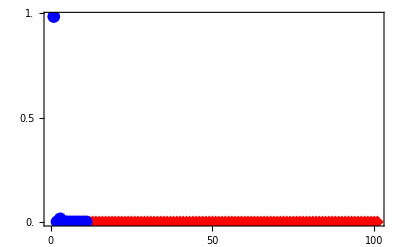

```mathematica
inslin=Show[{
ListPlot[nd[100,-1.`50,0.2`50],PlotMarkers->{"◆",13},PlotRange->All,PlotStyle->Red,PlotTheme->"Default",Frame->True,FrameTicks->{{Range[0,1,0.5],None},{Range[0,100,50],None}},Evaluate@font,Mesh->All],
ListLinePlot[nd[10,-1.`50,0.2`50],PlotMarkers->{"•",13},PlotStyle->Blue,Mesh->All]}]
```

```mathematica
illustrationcomp=Show[{
ListPlot[nd[10,-1.`50,0.2`50],Mesh->All,PlotRange->{{0.7,11.3},Automatic},
	ScalingFunctions->"Log",PlotMarkers->{"◆",13},PlotStyle->Blue,PlotTheme->"Default",
	FrameTicks->{{{{10^0,MaTeX["1"]},{10^-3,MaTeX["10^{-3}"]},{10^-6,MaTeX["10^{-6}"]},{10^-9,MaTeX["10^{-9}"]},{10^-12,MaTeX["10^{-12}"]}},None},{Transpose@{Range[1,11,1],Range[0,10,1]},None}},Method->{"ShrinkWrap"->True},PlotLegends->Placed[PointLegend[{MaTeX["N=10"]}],{0.15,0.4}]],
ListPlot[nd[100,-1.`50,0.2`50],Mesh->All,
	ScalingFunctions->"Log",PlotMarkers->{"•",13},PlotStyle->Red,PlotLegends->Placed[PointLegend[{MaTeX["N=100"]}],{0.16,0.3}]],
Plot[Exp[-2.4( x-1)],{x,1,11},ScalingFunctions->"Log",PlotStyle->{Blue,Dashed},PlotLegends->Placed[LineLegend[{MaTeX["\\exp(-2.4 n_t)"]},LegendMarkerSize->15],{0.19,0.2}]],
Plot[Exp[-1.9( x-1)],{x,1,11},ScalingFunctions->"Log",PlotStyle->{Red,Dashed},PlotLegends->Placed[LineLegend[{MaTeX["\\exp(-1.9 n_t)"]},LegendMarkerSize->15],{0.19,0.1}]]
},
FrameLabel->{"",""},Frame->True,PlotRangeClipping->False,Evaluate@font,
Epilog->{
Text[MaTeX["n_t"],{6,-33.5}],Text[Style[".",White],{6,-34.}],Text[Rotate[MaTeX["p"],π/2],{-0.65,-13.5}],Text[Style[".",White],{-0.76,-13.5}],
Inset[inslin,{9.05,-5.62},Automatic,Scaled[0.45]]
},ImageSize->337
]
```

-Graphics-

```mathematica
Export["/Users/strelda/Library/Mobile Documents/com~apple~CloudDocs/Files/synced Documents/phd/our/Quantum geometry of critical bosonic systems/img/vector_components.pdf",illustrationcomp,ImageResolution->1800];
```

```mathematica
data100=Transpose@{Range[1,21,2],Log@nd[100,-1.`100,0.2`100][[1;;21;;2]]};
```

```mathematica
fit100=NonlinearModelFit[data100, -a(x-1),{a},x,WorkingPrecision->40]
```

FittedModel[-1.94930110510303182695694638800629359599 (-1+x)]

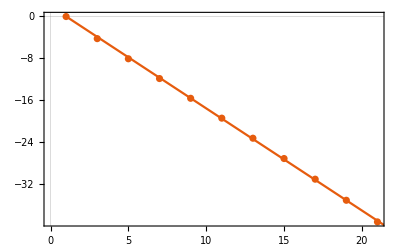

```mathematica
Show[{ListPlot[data100],Plot[fit100[x],{x,1,101}]}]
```

```mathematica
illustrationcomp=Module[{opt,opt12,opt3,optInset,p1,p2,p3,p1Inset,p2Inset,p3Inset},
opt={PlotRange->{All,All},ScalingFunctions->"Log"};
opt12=Flatten@{opt,FrameLabel->MaTeX/@{"","|\\psi_{HB}^{(i)}|^2"}};
opt3=Flatten@{opt,FrameLabel->MaTeX/@{"i","|\\psi_{HB}^{(i)}|^2"}};
optInset={PlotRange->{{1,15},{10^-20,1}},ScalingFunctions->"Log"};

{p1Inset,p2Inset,p3Inset}=ListPlot[Abs[ToEigenbasis[{30,50,100}[[#]],3.`50,2.`50].gsHB[{30,50,100}[[#]],3.`50,2.`50]]^2,Evaluate@optInset,ImageSize->140]&/@Range[3];

{p1,p2,p3}=ListPlot[Abs[ToEigenbasis[{30,50,100}[[#]],3.`50,2.`50].gsHB[{30,50,100}[[#]],3.`50,2.`50]]^2,Evaluate@{opt12,opt12,opt3}[[#]],FrameLabel->MaTeX/@{"","|\\psi_{HB}^{(i)}|^2"},
Epilog->Inset[p1Inset,Scaled[{0.68,0.68}]]
]&/@Range[3];


ResourceFunction["PlotGrid"][{{p1},{p2},{p3}},Spacings->15]
]
```

### Metric tensor

```mathematica
optMetric={Evaluate@font,PlotRange->{{-2.,2.},Automatic,{-π/2,π/2}},PlotRangePadding->0,ColorFunction->ColorData[{"TemperatureMap",{-π/2,π/2}}],FrameLabel->None,FrameTicks->{{Range[-5,5,1],None},{Range[-4,4,1],None}},ColorFunctionScaling->False,AspectRatio->1.7/7};
```

```mathematica
tQ=Quiet@Flatten[ParallelTable[{λ,χ,If[Phase1[λ,χ],{{0,0},{0,0}},10 gHB[10,λ,χ]/.Indeterminate->0]},{χ,-2.,2.,4/501},{λ,-2.,2.,4/501}],1];
```

```mathematica
{ggAHB,ggBHB,ggCHB}=ParallelTable[
ListDensityPlot[{ExtractIndexAtan[tQ,1,1],ExtractIndexAtan[tQ,1,2],ExtractIndexAtan[tQ,2,2]}[[i]],TicksStyle->Black,Evaluate@optMetric,PlotRangeClipping->False],
{i,1,3}];
```

```mathematica
barA=BarLegend[{"Temperature",{-π/2,π/2}},LegendLayout->"Row",Evaluate@font,LegendMarkerSize->220,Ticks->{{-0.7854,"-π/4"},{-1.57,"-π/2"},{0,0},{0.7854,"π/4"},{1.57,"π/2"}}];
```

```mathematica
ggabc=Quiet@ResourceFunction["PlotGrid"][{{ggAHB},{ggBHB},{ggCHB}},ImageMargins->10,
PlotLabels->Placed[MaTeX/@{"g_{\\kappa\\kappa}","g_{\\kappa\\chi}","g_{\\chi\\chi}"},{0.95,0.88}]];
```

```mathematica
plmetric=ImageCrop@Show[{
GraphicsColumn[{ggabc,Row@{Spacer[6],barA}},Spacings->8],
Graphics[Inset[MaTeX["\\kappa"],{195,-282}]],
Graphics[Inset[Rotate[MaTeX["\\chi"],-π/2],{5,-214}]],
Graphics[Inset[Rotate[MaTeX["\\chi"],-π/2],{5,-133}]],
Graphics[Inset[Rotate[MaTeX["\\chi"],-π/2],{5,-51}]],
Graphics[Inset[MaTeX["\\arctan(10\; \\mathbf g_{\\mu\\nu})"],{45,-302}]]
},ImageSize->340]
```

-Graphics-

```mathematica
Export["/Users/strelda/synced Documents/phd/our/Quantum geometry of critical bosonic systems/img/metric_HB_10.pdf",plmetric,"AllowRasterization"->True,ImageResolution->3000];
```

### Metric tensor error

```mathematica
tQE=Quiet@Flatten[ParallelTable[{λ,χ,If[Phase1[λ,χ],{{1.,1.},{1.,1.}},Abs[1.-(gHB[10,λ,χ]/.Indeterminate->0)/(gNumeric[10,λ,χ]/10)]]},{χ,-2.,2.,4/121},{λ,-2.,2.,4/121}],1];
```

```mathematica
barA=BarLegend[{ColorData[{"GrayTones",{1,0}}],{0,1.}},LegendLayout->"Row",Evaluate@font,LegendMarkerSize->220,Ticks->Range[0,1,0.5]]
```

```mathematica
optMetricError={Evaluate@font,PlotLegends->False,PlotRange->{0,1.},ColorFunction->(*ColorData[{"TemperatureMap",{-1,1}}]*)ColorData[{"GrayTones",{1,0}}],ColorFunctionScaling->False,
Epilog->{Text[Rotate[MaTeX["\\chi"],π/2],{-2.32,0.}],Text[MaTeX["\\kappa"],{0,-3.3}]},FrameLabel->{"",""},FrameTicks->{{Range[-2,2,1],None},{Range[-2,2,1],None}},
PlotRangePadding->0,(*ScalingFunctions->"Log",*)PlotRangeClipping->False,FrameLabel->None,AspectRatio->1.7/7,FrameLabel->MaTeX/@{"\\kappa","\\chi"}};
{ggAHB,ggBHB,ggCHB}=ParallelTable[
ListDensityPlot[{ExtractIndex[tQE,1,1],ExtractIndex[tQE,1,2],ExtractIndex[tQE,2,2]}[[i]],Evaluate@optMetricError,ClippingStyle->Automatic],
{i,1,3}];
```

```mathematica
ggCHB1=Show[ggCHB,ListPlot[{{{1.5,0.5}},{{-1.5,1.5}},{{1,1}}}[[#]],PlotStyle->{Red,Darker@Green,Blue}[[#]],PlotMarkers->{{"★","•","◆"}[[#]],16}]&/@Range[3]]
```

-Graphics-

```mathematica
ggabc=Quiet@ResourceFunction["PlotGrid"][{{ggAHB},{ggBHB},{ggCHB1}},ImageMargins->0,
PlotLabels->Placed[MaTeX/@{"g_{\\kappa\\kappa}^{rel}","g_{\\kappa\\chi}^{rel}","g_{\\chi\\chi}^{rel}"},{0.96,0.86}]];
metricerrorPlot=ImageCrop@Show[{
GraphicsColumn[{ggabc,Row@{Spacer[18],barA}},Spacings->-14],Graphics@Inset[MaTeX["g^{rel}_{\\mu\\nu}"],{86,-273}]
},ImageSize->360]
```

-Graphics-

```mathematica
Export["/Users/strelda/synced Documents/phd/our/Quantum geometry of critical bosonic systems/img/metric_HB_error.pdf",metricerrorPlot,"AllowRasterization"->True,ImageResolution->1000];
```

```mathematica
gHBConvergence[λ_,χ_,i_,j_]:=Quiet@ParallelTable[{n,Abs[1.-(gHB[n,λ,χ][[i,j]]/.Indeterminate->0)/(gNumeric[n,λ,χ][[i,j]]/n)]},{n,5,60,1}];
```

```mathematica
Abs[1.-(gHB[1500,1.5,0.5][[2,2]]/.Indeterminate->0)/(gNumeric[1500,1.5,0.5][[2,2]]/1500)]
```

0.133318

```mathematica
Abs[1.-(gHB[1500,-1.5,1.5][[2,2]]/.Indeterminate->0)/(gNumeric[1500,-1.5,1.5][[2,2]]/1500)]
```

0.163907

```mathematica
Abs[1.-(gHB[1500,1.,1.][[2,2]]/.Indeterminate->0)/(gNumeric[1500,1.,1.][[2,2]]/1500)]
```

0.0248375

```mathematica
plotIndex[i_,j_]:=ListPlot[
{gHBConvergence[1.5,0.5,i,j],gHBConvergence[-1.5,1.5,i,j],gHBConvergence[1.,1.,i,j]},
PlotStyle->{Red,Darker@Green,Blue},PlotMarkers->{"★","•","◆"},
Axes->False,PlotTheme->"Detailed",Evaluate@font,PlotRangeClipping->False,PlotRangePadding->0,Mesh->All,ImageSize->320,
PlotRange->{{4,61},{-0.02,0.33}},FrameTicks->{{Range[0,0.5,0.1],None},{Range[0,100,20],None}},GridLines->{None,{0.13,0.16,0.025}},
AspectRatio->1/3,FrameLabel->MaTeX/@{"",""},PlotLegends->Placed[PointLegend[{"(1.5,0.5)","(-1.5,1.5)","(1,1)"},LegendLayout->{"Row",1}],{0.6,0.85}],
Epilog->{Text[MaTeX["N"],{32.5,-0.1}],Text[Rotate[MaTeX["g_{\\chi\\chi}^{rel}"],π/2],{-2,0.155}]}]
```

```mathematica
pAC=plotIndex[2,2]
```

-Graphics-

```mathematica
Export["/Users/strelda/synced Documents/phd/our/Quantum geometry of critical bosonic systems/img/metric_HB_error_N.pdf",pAC,"AllowRasterization"->True,ImageResolution->3000];
```

```mathematica
pAA=plotIndex[1,1]
pAB=plotIndex[1,2]
```

-Graphics-

-Graphics-

### Ricci

```mathematica
tR1=Quiet@Flatten[ParallelTable[{λ,χ,RicciScalarHB[10,λ,χ]},{χ,-1.4,-0.01,1.4/4},{λ,-2,2,4/4}],1];
tR2=Quiet@Flatten[ParallelTable[{λ,χ,RicciScalarHB[10,λ,χ]},{χ,0.01,1.4,1.4/4},{λ,-2,2,4/4}],1];
tR=Join[[tR1,tR2]]
```

$Aborted

$Aborted

Part::pkspec1: The expression tR1 cannot be used as a part specification.

Join⟦tR1,tR2⟧

```mathematica
ListDensityPlot[ExtractIndexAtan[tR,1,1],TicksStyle->Black,Evaluate@optMetric,PlotRangeClipping->False]
```

# Heff using HB

## Simplify Heff

```mathematica
HeffAlongProtocol[λ_,χ_,τA_,τB_,n_,dΛ_]=Block[{a,b,c,d,ss,su,sv,suD,svD,u,v,α,β,h11,h12,h22,h11D,h12D,h22D,AHA,AHB,BHB,ADHA,ADHB,BDHB,heff1},
(*Calculate the Heff matrix from the knowledge of HB ground state in phase I (A) and phase II (B). Result is a 2x2 matrix, a function of λ,χ,τA,τB,dΛ,n
       τA - value of τ of HB approdximation in phase A, needs to be calculated using minCoord[λA,χA],
       τB - value of τ of HB approdximation in phase B, needs to be calculated using minCoord[λB,χB],
dΛ={λ,χ}-{λc,χc} - direction of protocol at QPT, vector from QPT (marked by c), its norm is the distance,
         n - dimension of H which is being approximated.
*)

(*Define the bosonic Hamiltonian H which is being approximated, u are coefficients for two particle interaction, v for four particle interactions. Indices are 0,1 for s,t bosons resp.*)

u=Table[0,{i,1,2},{j,1,2}];
u[[1,1]]=-1/2;
u[[2,2]]=1/2-χ^2/n;
u[[1,2]]=-χ/(2n);
u[[2,1]]=-χ/(2n);
If[modelWithJy,
u[[1,2]]=-χ/(2n)+(λ I)/(4n);
u[[2,1]]=-χ/(2n)-(λ I)/(4n);
];
v=Table[0,{i,1,2},{j,1,2},{k,1,2},{l,1,2}];
v[[2,2,1,1]]=v[[1,1,2,2]]=-λ/(4n);
v[[2,1,1,2]]=(-2λ)/(4n);
v[[2,2,1,2]]=v[[2,1,2,2]]=-χ/n;
v[[2,2,2,2]]=-χ^2/n;

(*Define the HB parametrization at two phases. Here α is in Phase I, β in Phase II.*)
α=1/(√(1+Abs[τA]^2)){1,τA};
β=1/(√(1+Abs[τB]^2)){1,τB};

(*Define matrix elements*)
ss[a_,b_]:=Sum[Conjugate[a[[i]]]b[[i]],{i,1,2}];
su[a_,b_]:=Sum[u[[i,j]]Conjugate[a[[i]]]b[[j]],{i,1,2},{j,1,2}];
sv[a_,b_,c_,d_]:=Sum[v[[i,j,k,l]]Conjugate[a[[i]]]Conjugate[b[[j]]]c[[k]]d[[l]],{i,1,2},{j,1,2},{k,1,2},{l,1,2}];

AHA=n(su[α,α]+(n-1)sv[α,α,α,α]);
AHB=n su[α,β] ss[α,β]^(n-1)+n(n-1)sv[α,α,β,β] ss[α,β]^(n-2);
BHB=n(su[β,β]+(n-1)sv[β,β,β,β]);


(*0. order*)
h11=1/(1-Abs[ss[α,β]^n]^2)(AHA-2Re[ss[β,α]^n AHB]+Abs[ss[β,α]^n]^2 BHB);
h12=1/(√(1-Abs[ss[α,β]^n]^2))(AHB-ss[α,β]^n BHB);
h22=BHB;


(*1. order*)
(*suD[a_,b_]:=Sum[{D[u[[i,j]],λ],D[u[[i,j]],χ]}.dΛ Conjugate[a[[i]]]b[[j]],{i,1,2},{j,1,2}];
svD[a_,b_,c_,d_]:=Sum[{D[v[[i,j,k,l]],λ],D[v[[i,j,k,l]],χ]}.dΛ Conjugate[a[[i]]]Conjugate[b[[j]]]c[[k]]d[[l]],{i,1,2},{j,1,2},{k,1,2},{l,1,2}];

ADHA=n(suD[α,α]+(n-1)svD[α,α,α,α]);
ADHB=n suD[α,β] ss[α,β]^(n-1)+n(n-1)svD[α,α,β,β] ss[α,β]^(n-2);
BDHB=n(suD[β,β]+(n-1)svD[β,β,β,β]);

h11D=1/(1-Abs[ss[α,β]^n]^2)(ADHA-2Re[ss[β,α]^n ADHB]+Abs[ss[β,α]^n]^2 BDHB);
h12D=1/(√(1-Abs[ss[α,β]^n]^2))(ADHB-ss[α,β]^n BDHB);
h22D=BDHB;*)


(*Add terms together*)
(*heff1={{0,h12},{Conjugate@h12,0}}+{{h11D,0},{0,h22D}};*)
(*heff1={{0,h12},{Conjugate@h12,0}}+1/2{{h11D,h12D},{Conjugate@h12D,h22D}};*)
heff1={{h11,h12},{Conjugate@h12,h22}};
heff1  (*+{{-n/2,0},{0,-n/2}}*)
];
```

## Find Heff along linear protocol or perpendicular line

#### Define linear protocol

The intersection with QPT for line parametrization χ = aλ + b is at a λQ+b==√((λQ-1)/(λQ-2))has candidates λQ[a_,b_]:=λQ/.Solve[a λQ+b==√((λQ-1)/(λQ-2)),λQ,Assumptions->λ<1.1], but we solve it numerically using Solve.
Line from {0, 0} to {1, 1/2} . Parametrization using line is a = 1/2, b = 0:

```mathematica
protocolLine[s_]:={s,s}
```

```mathematica
protocolLineIntersectAt=s/.Quiet@Solve[protocolLine[s][[2]]==qptA[protocolLine[s][[1]]],s][[1]]
```

0.554958

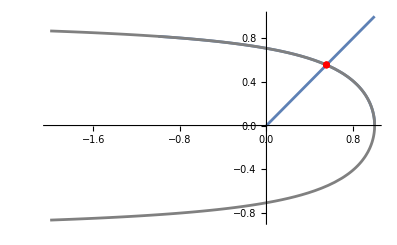

```mathematica
Show[Plot[qpt[λ],{λ,-1,1}],ParametricPlot[protocolLine[s],{s,0,1}],Plot[{qpt[λ],-qpt[λ]},{λ,-2,1},PlotStyle->Gray],ListPlot[{protocolLine[protocolLineIntersectAt]},PlotStyle->Red],PlotRange->All]
```

#### Calculate spectrum of Heff along linear protocol

```mathematica
eigenLine[s_?NumericQ,n_?NumericQ]:=Module[{λ,χ,λA,χA,λB,χB,dΛ},
(*Calculate eigenvalues of Heff approximating dimension n along the line protocolLine at point s. 
n - dimension of approximated Hamiltonian,
   s - protocol parametrization from 0 to 1.
*)
{λ,χ}=protocolLine[s];
Sort@Eigensystem@Heff[{λ,χ},n] 
]
```

```mathematica
ensApprox[n_,prec_,plotMin_:0,plotMax_:1]:=Module[{tab},
(*Calculate eigenvalues along protocol defined in eigenLine along the path between s∈{plotMin,plotMax}.*)
tab=Transpose@ParallelTable[Flatten@{s,eigenLine[s,n][[1]]},{s,plotMin,plotMax,(plotMax-plotMin)/prec}];
ListLinePlot[{Transpose@tab[[{1,2}]],Transpose@tab[[{1,3}]]},PlotRange->All,ImageSize->Medium,Frame->True,PlotLabel->n,FrameLabel->{"s","E"}]
]
```

#### Find closest perpendicular point to QPT

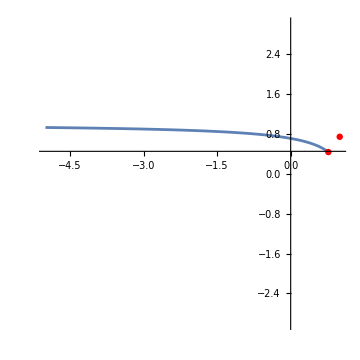
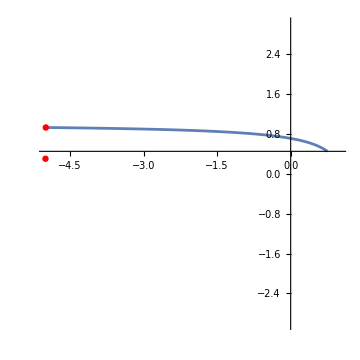

```mathematica
plot[λ_,χ_]:=Show[{Plot[qpt[l],{l,-5,1}],ListPlot[{{λ,χ},perpendicularCoord[λ,χ]},PlotStyle->Red]},PlotRange->{{-5,1},{-3,3}},AspectRatio->1,ImageSize->Medium]
{plot[1,0.74],plot[-5,0.3]}
```

#### Define Heff[λ_,χ_,n_], endifHeff[λ_,χ_,n_]

```mathematica
Heff[λ_?NumericQ,χ_?NumericQ,n_?NumericQ]:=Block[{τA,τB,λA,λB,χA,χB,dΛ,λc,χc,s,ϵ},
(*Effective Hamiltonian as a function of {λ,χ} and dimension of H. Calculates τA,τB in the vicinity of QPT and determines the direction of protocol.*)

(*Option1: Distance of {λ,χ} from line with QPT intersection.*)
(*{λA,χA}=protocolLine[protocolLineIntersectAt-ϵ];
{λB,χB}=protocolLine[protocolLineIntersectAt+ϵ];
dΛ={λ,χ}-protocolLine[protocolLineIntersectAt];*)

(*Option2: for every point λ,χ find the perpendicular vector to QPT and assume this direction as the crossing direction*)
(*ϵ=0.02;
{λc,χc}=perpendicularCoord[λ,χ];
dΛ= Abs[{λ,χ}-{λc,χc}];

{λA,χA}={λc,χc}-ϵ dΛ;
{λB,χB}={λc,χc}+ϵ dΛ;

τA=tr+I ti/.Quiet@minCoord[λA,χA];
τB=tr+I ti/.Quiet@minCoord[λB,χB];*)


(*Option3: for every point λ,χ find the perpendicular vector to QPT and at that intersection λ calculate LimitToQPT[λ], which produces tr at point B, for A use coordinate {0,0}*)
{λc,χc}=perpendicularCoord[λ,χ];
dΛ={λ,χ}-{λc,χc};
τA=0;
τB=LimitToQPT[λc];

(*Option4: *)
(*{λc,χc}=perpendicularCoord[λ,χ];
dΛ={λ,χ}-{λc,χc};
τA=0;(*LimitToQPTBelow[λc];*)
τB=If[χ<qpt[λ],LimitToQPT[λc],tr/.minCoord[λ,χ]];*)


(*{λ,χ,τA,τB,n,dΛ}*)
HeffAlongProtocol[λ,χ,τA,τB,n,dΛ]
]
```

```mathematica
(*Calculate the energy difference E1-E0 at {λ,χ} and dimension n for Heff and distance from QPT ϵ for Subscript[ψ, A],Subscript[ψ, B]*)
endifHeff[λ_?NumericQ,χ_?NumericQ,n_?NumericQ]:=Abs[Differences[Sort@Eigenvalues[Heff[λ,χ,n]]][[1]]]
```

## Comparison of energies and LimitToQPT

### Analysis

```mathematica
nn=10;
```

```mathematica
jj=nn/2;
f[mp_,m_]:=Hd[jj,mp,jj,m];
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
```

```mathematica
energyMin[λ_?NumericQ]:=Module[{χ0},
(*Find the energy minimum corresponding to the minimial line for specific λ*)
χ0=√((λ-1)/(λ-2));(*initial point for minimization*)
χ/.Quiet@FindMinimum[{endifH[λ,χ]&&0.01<χ<1.5},{χ,χ0},WorkingPrecision->workingprecision,Method->"ConjugateGradient"][[2]]
]
(*Find the minimal line of Heff*)
energyMineff[λ_?NumericQ]:=Module[{χ0},
(*Find the energy minimum corresponding to the minimial line of Heff for specific λ and distance from QPT ϵ for Subscript[ψ, A],Subscript[ψ, B]*)
χ0=√((λ-1)/(λ-2));(*initial point for minimization*)
χ/.Quiet@FindMinimum[{endifHeff[λ,χ,nn]},{χ,χ0},WorkingPrecision->workingprecision,Method->"Newton"][[2]]
]
```

```mathematica
trustedMinimumλ=-2.3;
```

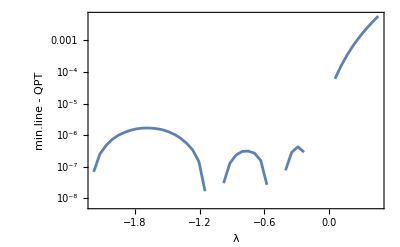

```mathematica
(*Difference of Minimal line H and QPT*)
ListLinePlot[ParallelTable[{λ,Quiet@energyMin[λ]-qpt[λ]},{λ,trustedMinimumλ,0.5,-trustedMinimumλ/40}],Evaluate@plot1,ScalingFunctions->"Log",FrameLabel->{"λ","min.line - QPT"}]
```

```mathematica
(*Interpolate the minimal line depenence for H and Heff*)
order=10;
```

```mathematica
(*precalculate Minimal line for H and Heff*)
minlinetab=Table[{λ,energyMin[λ]},{λ,trustedMinimumλ,0.5,3/60}];
```

```mathematica
minLine[λ_]:=Interpolation[minlinetab,InterpolationOrder->order][λ]
```

```mathematica
minlineefftab=;(*ParallelTable[{λ,Quiet@energyMineff[λ]},{λ,trustedMinimumλ,0.5,3/39}] for nn=10*)
```

```mathematica
minLineeff[λ_]:=Interpolation[minlineefftab,InterpolationOrder->order][λ]
```

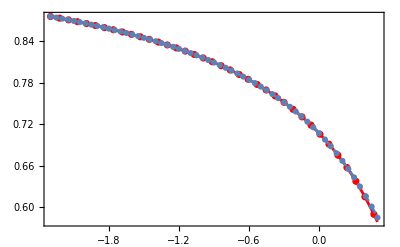

```mathematica
Show[{ListPlot[minlineefftab,PlotStyle->Red],Plot[minLineeff[λ],{λ,trustedMinimumλ,0.5},PlotStyle->Red],
ListPlot@minlinetab,Plot[minLine[λ],{λ,trustedMinimumλ,0.5},PlotStyle->Dashed]},Evaluate@plotOptions,PlotRange->All]
```

```mathematica
(*Limit from above at λ to the QPT, works for λ>1*)
LimitToQPTN[λ_?NumericQ]:=Quiet[NLimit[tr/.minCoord[λ,χ],χ->minLineeff[λ],Direction->-1,WorkingPrecision->workingprecision]];
```

```mathematica
(*for λ<-2.3, the numerics becomes problematic, workingprecision in minCoord needs to be increased if wanted to go below*)
limitToQPTtab=;(*Quiet@ParallelTable[{λ,LimitToQPTN[λ]},{λ,trustedMinimumλ,0.55,2/50}]; for nn=10*)
```

```mathematica
LimitToQPT[λ_]:=Interpolation[limitToQPTtab,InterpolationOrder->10][λ]
```

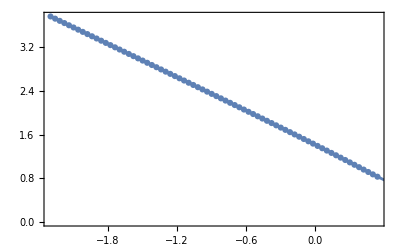

```mathematica
Quiet@Show[{ListPlot[limitToQPTtab],Plot[LimitToQPT[λ],{λ,trustedMinimumλ,1}]},Frame->True,FrameLabel->MaTeX/@{"\\kappa","\\tau"},Axes->False]
```

### Energy difference along the minimal line

```mathematica
(*Energy difference for H*)
de2=ParallelTable[{λ,endifH[λ,energyMin[λ]]},{λ,trustedMinimumλ,0.5,-trustedMinimumλ/350}];
```

```mathematica
(*Energy difference for Heff along minimal line energyMin[λ], or Heff minimum energyMineff[λ,ϵg]*)
de2eff=ParallelTable[{λ,endifHeff[λ,minLineeff[λ](*minLineeff[λ],energyMineff[λ]*),nn]},{λ,trustedMinimumλ,0.5,-trustedMinimumλ/350}];
```

$Aborted

```mathematica
optionsAlongCrit={Evaluate@font,Frame->True,PlotRange->{-12,-2.2},AspectRatio->1/2,Axes->False,FrameLabel->MaTeX/@{"\\kappa","\\log(E_1-E_0)"},ImageSize->280,PlotRangePadding->0,FrameTicks->{{Range[-50,0,2],None},{Range[-3,1,0.5],None}}};
```

SetPrecision::precsm: Requested precision 5 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of SetPrecision::precsm will be suppressed during this calculation.

```mathematica
pl[de_,deeff_]:=Show[{
ListLinePlot[de,ScalingFunctions->"Log",PlotStyle->{{Black,Dashed}}],
ListLinePlot[deeff,PlotStyle->Red,ScalingFunctions->"Log"]
},Evaluate@optionsAlongCrit]
```

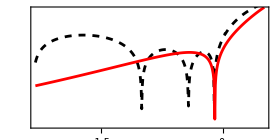

```mathematica
alongpl=pl[de2,de2eff]
```

```mathematica
Export["/Users/strelda/synced Documents/phd/our/Quantum geometry of critical bosonic systems/img/energy_along_minimal_lines.pdf",alongpl,"AllowRasterization"->True,ImageResolution->800];
```

### difference of energy difference between H and Heff as a densityPlot

```mathematica
(*Energy difference for H*)
endifdif=Flatten[ParallelTable[{λ,χ,Abs[endifH[λ,χ]-Quiet@endifHeff[λ,χ,nn]]},{λ,trustedMinimumλ-0.1,0.3,-trustedMinimumλ/20},{χ,0.47,1.03,0.43/20}],1];
```

```mathematica
barr=BarLegend[{ColorData["GrayTones"],{0,1}},LegendMarkerSize->273,Ticks->{{0,"10^-6"},{0.333,"10^-4"},{0.666,"10^-2"},{1,"10^0"}},LegendLayout->"Column",Evaluate@font];
```

```mathematica
densopteff={PlotLegends->Placed[barr,{1,0.542}],PlotRangePadding->0,ColorFunction->"GrayTones",ScalingFunctions->"Log",ImageSize->345,Evaluate@font,FrameLabel->MaTeX/@{"\\kappa","\\chi"},FrameTicks->{{Range[0,1,0.1],None},{Range[-5,5,0.5],None}}};
endifdifplot=Show[
ListDensityPlot[endifdif,Evaluate@densopteff](*energy difference for H and Heffs*)
,ListPlot[diabolicPoints[nn],PlotStyle->Red,PlotMarkers->{cross,0.035}](*diabolic points*)
,ParametricPlot[{-3/7,χ},{χ,0.6,1},PlotStyle->{Blue,Dashed}]
(*ListLinePlot[minlinetab],(*Minimal line H*)*)
(*ListLinePlot[minlineefftab,PlotStyle->Magenta],(*Minimal line Heff*)*)
(*Plot[qpt[λ],{λ,-3,1},PlotStyle->{Dashed,Gray}],(*qpt*)*)
];
```

```mathematica
endifOpt={FrameLabel->None,PlotRangeClipping->False,Evaluate@plotOptions,PlotPoints->150,PerformanceGoal->"Quality",PlotRange->{-7,-2},ImagePadding->35,
Epilog->{Text[MaTeX["\\chi"],{0.8,-8.45}],Text[Rotate[MaTeX["E"],π/2],{0.51,-4.5}]},
FrameTicks->{{{-6,-4,-2},None},{{0.6,0.8,1},None}}
};
```

SetPrecision::precsm: Requested precision 5 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of SetPrecision::precsm will be suppressed during this calculation.

```mathematica
{ensCompare12,ensCompare3}=ParallelTable[Plot[{Sort[Eigenvalues[HC[-3/7,χ]]][[1;;2]],Sort[Eigenvalues[HC[-3/7,χ]]][[3]]}[[i]],{χ,0.6,1},PlotStyle->{Black,Thickness[0.009]},Evaluate@endifOpt],{i,1,2}]
```

{-Graphics-,-Graphics-}

```mathematica
ensCompareEff=Plot[Sort[Eigenvalues[Heff[-3/7,χ,nn]]],{χ,0.6,1},PlotStyle->{Blue,Dashed,Thickness[0.009]},Evaluate@endifOpt];
```

```mathematica
ensCompared=Show[{ensCompare3,ensCompare12,ensCompareEff},ImageSize->200];
endifdifplotFinal=Show[{
endifdifplot,
Graphics[Inset[ensCompared,{-1.3,0.635}]]
}]
```

-Graphics-

```mathematica
|Delta E-Delta Subscript[E, eff]|
```

```mathematica
Export["/Users/strelda/synced Documents/phd/our/Quantum geometry of critical bosonic systems/img/energy_difference_error.pdf",endifdifplotFinal,"AllowRasterization"->True,ImageResolution->1800];
```

### Energy difference as a densityPlot

```mathematica
(*Energy difference for H*)
endifHtab=Flatten[ParallelTable[{λ,χ,endifH[λ,χ]},{λ,-1,0,1/10},{χ,0.65,0.84,0.09/10}],1];
```

```mathematica
(*Energy difference for Heff*)
endifHefftab=Flatten[ParallelTable[{λ,χ,Quiet@endifHeff[λ,χ,nn]},{λ,-1,-0,1/60},{χ,0.7,0.86,0.16/60}],1];
```

$Aborted

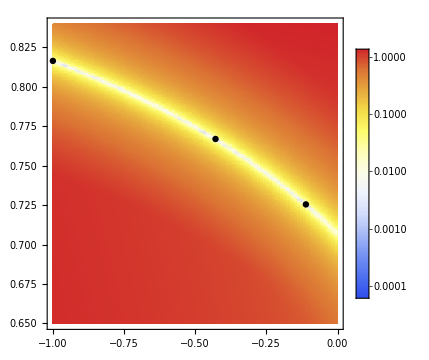
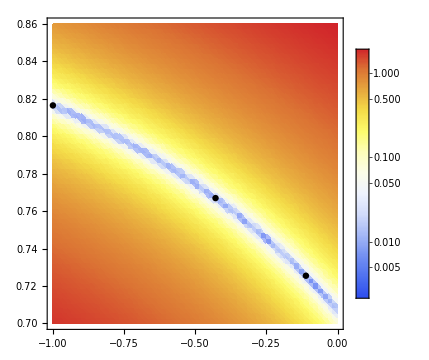

```mathematica
densopteff={PlotLegends->Automatic,ColorFunction->"TemperatureMap",ScalingFunctions->"Log"};
Show[
ListDensityPlot[#,Evaluate@densopteff],(*energy difference for H and Heffs*)
ListPlot[diabolicPoints[nn],PlotStyle->Black],(*diabolic points*)
(*ListLinePlot[minlinetab],(*Minimal line H*)*)
(*ListLinePlot[minlineefftab,PlotStyle->Magenta],(*Minimal line Heff*)*)
(*Plot[qpt[λ],{λ,-3,1},PlotStyle->{Dashed,Gray}],(*qpt*)*)
ImageSize->Medium]&/@{endifHtab,endifHefftab}
```

## Geometry of Heff

Set N at the beginning of notebook

```mathematica
(*nn=10; (*problem dimension*)*)
zoom=2; (*distance from the intersection of line with QPT*)
diff=20; (*plot precision*)
plotOptionsGeom={ColorFunction->"TemperatureMap",PlotLegends->Automatic,Evaluate@plotOptions};
```

### H

```mathematica
(*(*Along the line*)
c50={protocolLine[protocolLineIntersectAt][[1]],protocolLine[protocolLineIntersectAt][[2]]};
endifHTab=ParallelTable[{λ,χ,endifH[λ,χ]},{λ,c50[[1]]-zoom,c50[[1]]+zoom,(2zoom)/diff},{χ,c50[[2]]-zoom/5,c50[[2]]+zoom/5,(2zoom)/diff}];
endifHplot=ListDensityPlot[Flatten[endifHTab,1],Evaluate@plotOptionsGeom,ScalingFunctions->"Log"];*)
```

```mathematica
(*endifHplot=DensityPlot[endifH[λ,χ],{λ,-3,1},{χ,0,1.3},PlotPoints->3];*)
```

### Heff

```mathematica
(*(*along the line*)
endifHeffTab=ParallelTable[{λ,χ,Log@endifHeffN[λ,χ,nn,ϵ]},{λ,c50[[1]]-zoom,c50[[1]]+zoom,(2zoom)/diff},{χ,c50[[2]]-zoom/5,c50[[2]]+zoom/5,(2zoom)/diff}];
endifHeffplot=ListDensityPlot[Flatten[endifHeffTab,1],Evaluate@plotOptionsGeom];*)
```

```mathematica
(*endifHplot=DensityPlot[endifHeff[λ,χ,nn,ϵg],{λ,-3,1},{χ,0,1.3},PlotPoints->3]*)
```

### Metric tensor

#### Functions

```mathematica
DH1Ceff[λ_?NumericQ,χ_?NumericQ]:=ND[Heff[l,χ,nn],l,λ];
DH2Ceff[λ_?NumericQ,χ_?NumericQ]:=ND[Heff[λ,c,nn],c,χ];
```

```mathematica
gCeff[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,en,dim,eigNonSort,eig,g11,g12,g22,M1,M1T,M2,M2T,endif},
dim=2;

{enNonSort,eigNonSort}=Eigensystem[Heff[λ,χ,nn]];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];

M1=Conjugate[eig⟦1⟧].DH1Ceff[λ,χ].eig⟦#⟧&/@Range[2,dim];

M1T=Conjugate[eig⟦#⟧].DH1Ceff[λ,χ].eig⟦1⟧&/@Range[2,dim];

M2=Conjugate[eig⟦1⟧].DH2Ceff[λ,χ].eig⟦#⟧&/@Range[2,dim];
M2T=Conjugate[eig⟦#⟧].DH2Ceff[λ,χ].eig⟦1⟧&/@Range[2,dim];
endif=(en⟦1⟧-en⟦#⟧)^2&/@Range[2,dim];
g11=Re@Sum[(M1⟦i⟧M1T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g12=Re@Sum[(M1⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g22=Re@Sum[(M2⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
{{g11,g12},{g12,g22}}
]
G1eff[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,dg,gInv},
derTerms=10;
dg={ND[gCeff[l,χ],l,λ,Terms->derTerms],ND[gCeff[λ,c],c,χ,Terms->derTerms]};
gInv=1/2 Inverse[gCeff[λ,χ]];
{Sum[gInv[[1,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],Sum[gInv[[1,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],Sum[gInv[[1,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
G2eff[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,dg,gInv},
derTerms=10;
dg={ND[gCeff[l,χ],l,λ,Terms->derTerms],ND[gCeff[λ,c],c,χ,Terms->derTerms]};
gInv=1/2 Inverse[gCeff[λ,χ]];
{Sum[gInv[[2,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],Sum[gInv[[2,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],Sum[gInv[[2,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
```

#### Analysis

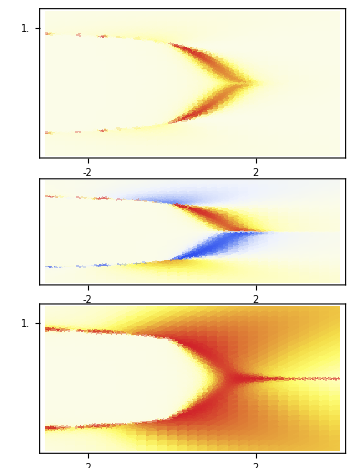
Compare to the N = 10 metric tensor elements
-Graphics-

```mathematica
gcTabgenerate[λmin_,λmax_,χmin_,χmax_,prec_]:=Flatten[ParallelTable[{x,y,ArcTan[Quiet@gCeff[x,y]](*Log[Abs[gC[x,y]-gCeff[x,y]]]*)},{x,λmin,λmax,(λmax-λmin)/prec},{y,χmin,χmax,(χmax-χmin)/prec}],1];
```

```mathematica
gcTabeff=gcTabgenerate[-0.1215,-0.089,0.718,0.732,30];
```

```mathematica
optgeff={Evaluate@font,PlotRange->Full,PlotLegends->False,ColorFunction->"TemperatureMap"};
```

```mathematica
{gcTabx,gcTaby}={Transpose[gcTabeff][[1]],Transpose[gcTabeff][[2]]};
takeElem[i_,j_]:=Transpose[gcTabeff][[3]][[#]][[i,j]]&/@Range[Length[gcTabeff]]
plotElem[i_,j_]:=ListDensityPlot[Transpose@{gcTabx,gcTaby,takeElem[i,j]},FrameTicks->{{Range[0,1.5,0.01],None},{Range[-1,1,0.01],None}},Evaluate@optgeff]
```

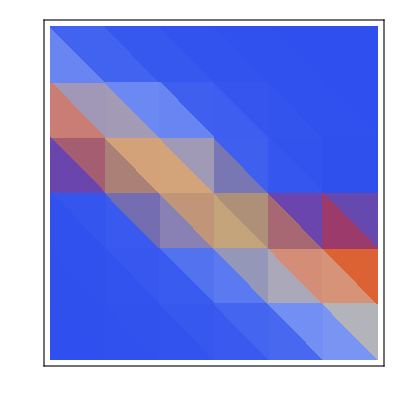
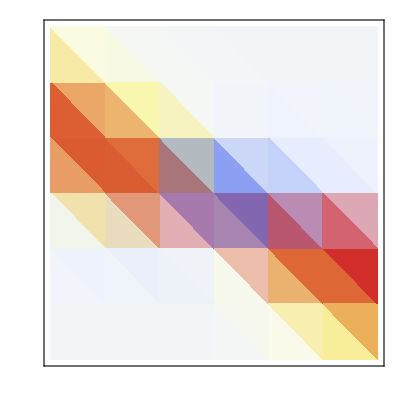
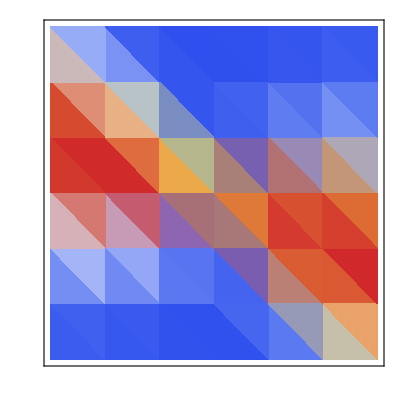

```mathematica
{{plotElem[1,1]},{plotElem[1,2]},{plotElem[2,2]}}
```

```mathematica
plA=ResourceFunction["PlotGrid"][{{plotElem[1,1]},{plotElem[1,2]},{plotElem[2,2]}},ImageSize->330,PlotLabels->Placed[MaTeX/@{"g_{\\kappa\\kappa}","g_{\\kappa\\chi}","g_{\\chi\\chi}"},{0.95,0.85}]]
plABC=PlotWithLegend[plA,barA]
```

```mathematica
{{-Graphics-}, {}}
```

### Metric and Christoffel

```mathematica
optDen={PlotRange->{-π/2,π/2},PlotRangePadding->0,ColorFunction->ColorData[{"TemperatureMap",{-π/2,π/2}}],FrameLabel->MaTeX/@{"\\kappa","\\chi"},FrameTicks->{{Range[-5,5,1],None},{Range[-4,4,1],None}},ColorFunctionScaling->False,AspectRatio->1.7/7};
```

```mathematica
barA=BarLegend[{"Temperature",{-π/2,π/2}},LegendLayout->"Row",Evaluate@font,LegendMarkerSize->220,Ticks->{{-0.7854,"-π/4"},{-1.57,"-π/2"},{0,0},{0.7854,"π/4"},{1.57,"π/2"}}];
```

```mathematica
gamma111Tabgenerate[λmin_,λmax_,χmin_,χmax_,prec_]:=Flatten[ParallelTable[{x,y,ArcTan[Quiet@G1eff[x,y][[1]]]},{x,λmin,λmax,(λmax-λmin)/prec},{y,χmin,χmax,(χmax-χmin)/prec}],1];
```

```mathematica
densopteff={PlotLegends->Automatic(*Placed[barr2,Right]*),ColorFunction->"TemperatureMap",ScalingFunctions->"Log",ImageSize->270,Evaluate@font,FrameLabel->MaTeX/@{"\\kappa","\\chi"},FrameTicks->{{Range[0,1,0.05],None},{Range[-5,5,0.5],None}}};
```

```mathematica
ListDensityPlot[Transpose@{gcTabx,gcTaby,takeElem[1,1]takeElem[2,2]-takeElem[1,2]^2},PlotLegends->Automatic,PlotRange->All,PlotTheme->"Scientific"]
```

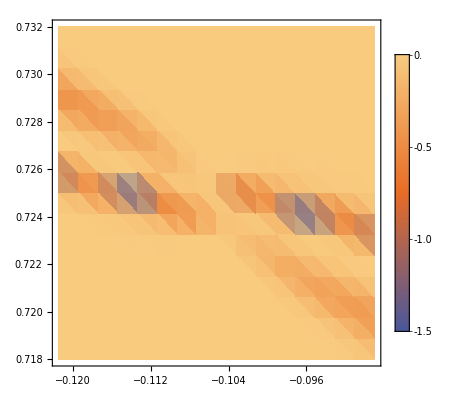

```mathematica
(*ggA=DensityPlot[ArcTan[gCeff[y,x]⟦1,1⟧],{y,-5,5},{x,0.1,3},PlotPoints->3,Evaluate@optDen];
ggB=DensityPlot[ArcTan[gCeff[y,x]⟦1,2⟧],{y,-5,5},{x,0.1,3},PlotPoints->3,Evaluate@optDen];
ggC=DensityPlot[ArcTan[gCeff[y,x]⟦2,2⟧],{y,-5,5},{x,0.1,3},PlotPoints->3,Evaluate@optDen];
plABC=plotGrid[{{ggA},{ggB},{ggC}},ggSize,ggSize*1.3,ImagePadding->50]*)
```

```mathematica
(*ggA=DensityPlot[ArcTan[gCeff[y,x]⟦1,1⟧],{y,-1,1},{x,0.3,1.1},Evaluate@optDen];
ggB=DensityPlot[ArcTan[gCeff[y,x]⟦1,2⟧],{y,-1,1},{x,0.3,1.1},Evaluate@optDen];
ggC=DensityPlot[ArcTan[gCeff[y,x]⟦2,2⟧],{y,-1,1},{x,0.3,1.1},Evaluate@optDen];
plABC=plotGrid[{{ggA},{ggB},{ggC}},ggSize,ggSize*1.3,ImagePadding->50]*)
```

```mathematica
(*DensityPlot[ArcTan@Det@gCeff[λ,χ],{λ,-3,3},{χ,-1.5,1.5},PlotRange->All,PlotLegends->Automatic]*)
```

### Geodesics

#### Define functions

```mathematica
GetMaxTimeFromSolve[sol_]:=sol[[1,1,2,1,1,2]];

ColorSpeed[sol_,t_]:=First[{√(λ'[t]^2+χ'[t]^2)}/.sol][[1]]
PlotSolsSpeed[solMulti_,style_:"None"]:=Module[{numPaths},
numPaths=Length[solMulti];
Table[ParametricPlot[
{λ[t],χ[t]}/.solMulti[[i]],{t,0,GetMaxTimeFromSolve[solMulti[[i]]]}
,PlotRange->All,Frame->True,PlotStyle->{Thickness[0.003],ToExpression@style},AspectRatio->1,
ColorFunction->Function[{x,y,t},Blend[{Black,Red},ColorSpeed[solMulti[[i]],t]]],ColorFunctionScaling->False
],{i,1,numPaths}]
]
```

```mathematica
eq={
λ''[t]+G1[λ[t],χ[t]].{ λ'[t]^2,2 λ'[t]χ'[t], χ'[t]^2}==0,
χ''[t]+G2[λ[t],χ[t]].{ λ'[t]^2,2 λ'[t]χ'[t], χ'[t]^2}==0
};
singStop=10^-2;
stopEvent={WhenEvent[-10>λ[t]>10||-10>χ[t]>10,"StopIntegration"]};
cauchy[l1_,x1_,l2_,x2_]:={λ[0]==l1,χ[0]==x1,λ'[0]==l2,χ'[0]==x2};
```

```mathematica
(*
geodbgTab=Flatten[ParallelTable[{λ,χ,ArcTan@Det[gCeff[λ,χ]]},{λ,-5,5,10/diff},{χ,2/diff,2,2/diff}],1];
geodbg = ListDensityPlot[geodbgTab,Evaluate@font, PlotRange->Full,PlotLegends->Automatic,ColorFunction->ColorData[{"GrayTones",{1,0}}],FrameLabel->{-Graphics-,-Graphics-},PlotRange->Full,ImageSize->310];
PlotMulti[solMulti_]:=Show[{geodbg,PlotSolsSpeed[Reverse@Join[solMulti]],
Graphics[{White,Polygon[{{-100,-100},{-5,0},{10,0},{100,-100}}]}],
Graphics[{White,Polygon[{{100,-100},{10,0},{10,1},{100,100}}]}],
Graphics[{White,Polygon[{{100,100},{10,1},{-5,1},{-100,100}}]}],
Graphics[{White,Polygon[{{-100,100},{-5,1},{-5,0},{-100,-100}}]}]},FrameTicks->{{Range[-10,10,0.25],None},{Range[-10,10,2],None}}]*)
```

#### Analysis

```mathematica
If[modelWithJy==True,
solMulti1=Quiet@ParallelTable[Quiet@NDSolve[
Join[eq,cauchy[-1,0.5,Cos[a],Sin[a]],stopEvent],{λ,χ},{t,0,30},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},PrecisionGoal->10,AccuracyGoal->10
],{a,0,2π,2π/10}];
Show[geodbg,PlotSolsSpeed[solMulti1]]
]
```

```mathematica
≥
```

0.80942721429281834631100317468002872838767464469691

$Aborted

$Aborted